# Gavish24: CEP at the limits:

RHS= (Λ-S μ-I1 S β_1-I2 S β_2-S Y1 β_1 η_1-S Y2 β_2 η_2+R1 θ_1+R2 θ_2+R θ_3
-I1 μ+I1 S β_1-I1 γ_1+S Y1 β_1 η_1
-Y1 μ-Y1 γ_1+I1 R2 β_1 σ_1+R2 Y1 β_1 η_1 σ_1
-R1 μ+I1 γ_1-R1 θ_1-I2 R1 β_2 σ_2-R1 Y2 β_2 η_2 σ_2
-I2 μ+I2 S β_2-I2 γ_2+S Y2 β_2 η_2
-Y2 μ-Y2 γ_2+I2 R1 β_2 σ_2+R1 Y2 β_2 η_2 σ_2
-R2 μ+I2 γ_2-R2 θ_2-I1 R2 β_1 σ_1-R2 Y1 β_1 η_1 σ_1
-R μ+Y1 γ_1+Y2 γ_2-R θ_3) has var {S,I1,Y1,R1,I2,Y2,R2,R} par{Λ,μ,β_1,β_2,γ_1,γ_2,η_1,η_2,θ_1,θ_2,θ_3,σ_1,σ_2}

minimal siphons {{I1,Y1},{I2,Y2}} Check siphon={True,True}

Infection species  at positions: {2,3,5,6}

DFE solution E0: {R→0,R1→0,R2→0,S→Λ/μ,I1→0,Y1→0,I2→0,Y2→0}

NGM K= ((S β_1)/(μ+γ_1) | (S β_1 η_1)/(μ+γ_1) | 0 | 0
(R2 β_1 σ_1)/(μ+γ_1) | (R2 β_1 η_1 σ_1)/(μ+γ_1) | 0 | 0
0 | 0 | (S β_2)/(μ+γ_2) | (S β_2 η_2)/(μ+γ_2)
0 | 0 | (R1 β_2 σ_2)/(μ+γ_2) | (R1 β_2 η_2 σ_2)/(μ+γ_2)) =((S β_1)/(μ+γ_1) | (S β_1 η_1)/(μ+γ_1) | 0 | 0
0 | 0 | 0 | 0
0 | 0 | (S β_2)/(μ+γ_2) | (S β_2 η_2)/(μ+γ_2)
0 | 0 | 0 | 0)

Reproduction functions R0A: {(β_1 (S+R2 η_1 σ_1))/(μ+γ_1),(β_2 (S+R1 η_2 σ_2))/(μ+γ_2)}

R0 at DFE: Max[(S β_1)/(μ+γ_1),(S β_2)/(μ+γ_2)]

Solve::svars: Equations may not give solutions for all "solve" variables.

Number of boundary systems= 2 ;first sys has 3 sols, E1 is {S→(μ+γ_1)/β_1,I1→-((μ^2-Λ β_1+μ γ_1) (μ+θ_1))/(μ β_1 (μ+γ_1+θ_1)),Y1→0,R1→-(γ_1 (μ^2-Λ β_1+μ γ_1))/(μ β_1 (μ+γ_1+θ_1)),R2→0,R→0} second sys has 3 sols, 
E2 is {S→(μ+γ_2)/β_2,R1→0,I2→-((μ^2-Λ β_2+μ γ_2) (μ+θ_2))/(μ β_2 (μ+γ_2+θ_2)),Y2→0,R2→-(γ_2 (μ^2-Λ β_2+μ γ_2))/(μ β_2 (μ+γ_2+θ_2)),R→0}

invasion nrs are{1.05556,1.58333}

equ: <|E0→{S→3.,I1→0,Y1→0,R1→0,I2→0,Y2→0,R2→0,R→0},E2→{S→2.,I1→0,Y1→0,R1→0,I2→0.555556,Y2→0,R2→0.444444,R→0},E4→{S→1.94424,I1→0.0569524,Y1→0.0120438,R1→0.022304,I2→0.538028,Y2→0.00617217,R2→0.411152,R→0.009108}|>

nbFP: 3

posEq: {{S→1.94424,I1→0.0569524,Y1→0.0120438,R1→0.022304,I2→0.538028,Y2→0.00617217,R2→0.411152,R→0.009108}}

var: {S,I1,Y1,R1,I2,Y2,R2,R}

Using parameter range: {1.5,6} for Λ

Continuing with parameter: Λ from 1.5 to 6

Starting equilibrium: {S→3.,I1→0,Y1→0,R1→0,I2→0,Y2→0,R2→0,R→0}

Found 21 equilibria along continuation curve

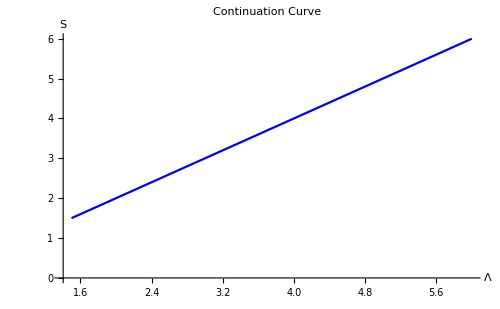

Positive equilibrium: {S→1.94424,I1→0.0569524,Y1→0.0120438,R1→0.022304,I2→0.538028,Y2→0.00617217,R2→0.411152,R→0.009108}

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];
Needs["EpidCRN1`"];
Needs["HopfR1`"];
?HopfR1`* 
(*Gavish two-strain model*)(*Test cont with real bdAnalEx outputs*)(*Your setup*)



RN={0->"S","S"+"I1"->2*"I1","S"+"Y1"->"Y1"+"I1","I1"->"R1","S"+"I2"->2*"I2","S"+"Y2"->"Y2"+"I2",
"I2"->"R2","R1"+"I2"->"I2"+"Y2","R1"+"Y2"->2*"Y2","Y2"->"R","R2"+"I1"->"I1"+"Y1","R2"+"Y1"->2*"Y1",
"Y1"->"R","R1"->"S","R2"->"S","R"->"S",
"S"->0,"I1"->0,"Y1"->0,"R1"->0,"I2"->0,"Y2"->0,"R2"->0,"R"->0};

rts={Λ,Subscript[β,1]*I1*S,Subscript[β,1]*Subscript[η,1]*Y1*S,Subscript[γ,1]*I1,Subscript[β,2]*I2*S,
Subscript[β,2]*Subscript[η,2]*Y2*S,Subscript[γ,2]*I2,Subscript[β,2]*Subscript[σ,2]*I2*R1,
Subscript[β,2]*Subscript[σ,2]*Subscript[η,2]*Y2*R1,Subscript[γ,2]*Y2,Subscript[β,1]*Subscript[σ,1]*I1*R2,
Subscript[β,1]*Subscript[σ,1]*Subscript[η,1]*Y1*R2,Subscript[γ,1]*Y1,Subscript[θ,1]*R1,Subscript[θ,2]*R2,
Subscript[θ,3]*R,μ*S,μ*I1,μ*Y1,μ*R1,μ*I2,μ*Y2,μ*R2,μ*R};


(*Get bdAnalEx outputs*)
{ngm, Jx, Jy, mSi, R0, R0A, E0, EA, E1, E2, RHS, var, cp, R12, R21, coP} = bdAnalEx[RN, rts];

par = Par[RHS, var];
(*extMat[RN]*)

(* Find equilibria *)
{equ,nbFP,posEq,var}=intEqV[RHS,var,coP];



(* Perform continuation analysis *)
curve = cont[RHS, var, equ, par, coP];
fpP=intEq[RHS,var,coP];
Print["Positive equilibrium: ",fpP[[1]] ]
```

## Search for Hopf Points:

bif param={β_1,β_2} coPsec = {Λ→3,μ→1,γ_1→1,γ_2→1,η_1→5,η_2→5/2,θ_1→1,θ_2→1/4,θ_3→1,σ_1→1,σ_2→1}p0={β_1→1/2,β_2→1}

p0 coordinates: {1/2,1} p1 coordinates: {3,3/4} p2 coordinates: {0.7,0.7} p0e coordinates: {1.46667,0.740667}

Scanning 25 points (wRan=0.5, hRan=0.8, hTol=0.5] for Hopf bifurcations...

11real solutions found

Positive solutions (coexistence): 0

No coexistence equilibrium found

12real solutions found

Positive solutions (coexistence): 0

No coexistence equilibrium found

12real solutions found

Positive solutions (coexistence): 0

No coexistence equilibrium found

12real solutions found

Positive solutions (coexistence): 0

No coexistence equilibrium found

13real solutions found

Positive solutions (coexistence): 0

No coexistence equilibrium found

12real solutions found

Positive solutions (coexistence): 0

No coexistence equilibrium found

10real solutions found

Positive solutions (coexistence): 0

No coexistence equilibrium found

11real solutions found

Positive solutions (coexistence): 0

No coexistence equilibrium found

15real solutions found

Positive solutions (coexistence): 0

No coexistence equilibrium found

13real solutions found

Positive solutions (coexistence): 0

No coexistence equilibrium found

11real solutions found

Positive solutions (coexistence): 0

No coexistence equilibrium found

11real solutions found

Positive solutions (coexistence): 0

No coexistence equilibrium found

10real solutions found

Positive solutions (coexistence): 1

Using equilibrium: {1.94424,0.0569524,0.0120438,0.022304,0.538028,0.00617217,0.411152,0.009108}

Eigenvalues: {-2.66938,-2.07006+0.527646 ⅈ,-2.07006-0.527646 ⅈ,-1.92603,-0.811347+0.630701 ⅈ,-0.811347-0.630701 ⅈ,-1.,-0.11587}

Result:Complex eigenvalues but not near Hopf conditions (stable spiral)

14real solutions found

Positive solutions (coexistence): 1

Using equilibrium: {1.30596,0.158498,0.0653923,0.0490442,0.804294,0.0302046,0.538808,0.0477984}

Eigenvalues: {-3.17295,-2.44131+0.857665 ⅈ,-2.44131-0.857665 ⅈ,-1.65405,-0.939813+0.864019 ⅈ,-0.939813-0.864019 ⅈ,-1.,-0.609676}

Result:Complex eigenvalues but not near Hopf conditions (stable spiral)

15real solutions found

Positive solutions (coexistence): 1

Using equilibrium: {0.999742,0.174621,0.104808,0.0445477,0.959681,0.0427626,0.600052,0.0737856}

Eigenvalues: {-3.65571,-2.74339+0.869409 ⅈ,-2.74339-0.869409 ⅈ,-1.24804+0.765768 ⅈ,-1.24804-0.765768 ⅈ,-1.07491+0.558606 ⅈ,-1.07491-0.558606 ⅈ,-1.}

Result:Complex eigenvalues but not near Hopf conditions (stable spiral)

13real solutions found

Positive solutions (coexistence): 0

No coexistence equilibrium found

13real solutions found

Positive solutions (coexistence): 0

No coexistence equilibrium found

10real solutions found

Positive solutions (coexistence): 1

Using equilibrium: {1.72015,0.284792,0.0490017,0.111942,0.467967,0.0304539,0.295971,0.0397278}

Eigenvalues: {-2.86779,-2.2926+0.995636 ⅈ,-2.2926-0.995636 ⅈ,-1.83508,-1.,-0.549046+0.746143 ⅈ,-0.549046-0.746143 ⅈ,-0.614294}

Result:Complex eigenvalues but not near Hopf conditions (stable spiral)

14real solutions found

Positive solutions (coexistence): 2

Using equilibrium: {1.17699,0.326082,0.112094,0.100632,0.729939,0.0624091,0.404602,0.0872513}

Eigenvalues: {-3.23706,-2.77598+1.18105 ⅈ,-2.77598-1.18105 ⅈ,-1.38092+0.353001 ⅈ,-1.38092-0.353001 ⅈ,-0.644008+1.02698 ⅈ,-0.644008-1.02698 ⅈ,-1.}

Result:Complex eigenvalues but not near Hopf conditions (stable spiral)

16real solutions found

Positive solutions (coexistence): 2

Using equilibrium: {0.912456,0.31324,0.15706,0.0794619,0.886005,0.0771583,0.457509,0.117109}

Eigenvalues: {-3.54271,-3.22086+1.14359 ⅈ,-3.22086-1.14359 ⅈ,-1.51989+0.700799 ⅈ,-1.51989-0.700799 ⅈ,-0.741507+1.11319 ⅈ,-0.741507-1.11319 ⅈ,-1.}

Result:Complex eigenvalues but not near Hopf conditions (stable spiral)

13real solutions found

Positive solutions (coexistence): 0

No coexistence equilibrium found

13real solutions found

Positive solutions (coexistence): 0

No coexistence equilibrium found

12real solutions found

Positive solutions (coexistence): 1

Using equilibrium: {1.5455,0.461011,0.0668868,0.181799,0.414064,0.0487067,0.224233,0.0577967}

Eigenvalues: {-2.98732,-2.46042+1.1907 ⅈ,-2.46042-1.1907 ⅈ,-1.75484,-0.537797+0.894004 ⅈ,-0.537797-0.894004 ⅈ,-1.,-0.776245}

Result:Complex eigenvalues but not near Hopf conditions (stable spiral)

15real solutions found

Positive solutions (coexistence): 1

Using equilibrium: {1.07496,0.459176,0.135981,0.141444,0.669889,0.0881443,0.318341,0.112063}

Eigenvalues: {-3.33653,-3.01091+1.36042 ⅈ,-3.01091-1.36042 ⅈ,-1.43738+0.512215 ⅈ,-1.43738-0.512215 ⅈ,-0.609105+1.169 ⅈ,-0.609105-1.169 ⅈ,-1.}

Result:Complex eigenvalues but not near Hopf conditions (stable spiral)

13real solutions found

Positive solutions (coexistence): 2

Using equilibrium: {0.842269,0.425726,0.184429,0.107537,0.824956,0.105326,0.364879,0.144877}

Eigenvalues: {-3.52372+1.32814 ⅈ,-3.52372-1.32814 ⅈ,-3.58876,-1.57368+0.772549 ⅈ,-1.57368-0.772549 ⅈ,-0.703011+1.2782 ⅈ,-0.703011-1.2782 ⅈ,-1.}

Result:Complex eigenvalues but not near Hopf conditions (stable spiral)

Found 0 Hopf points

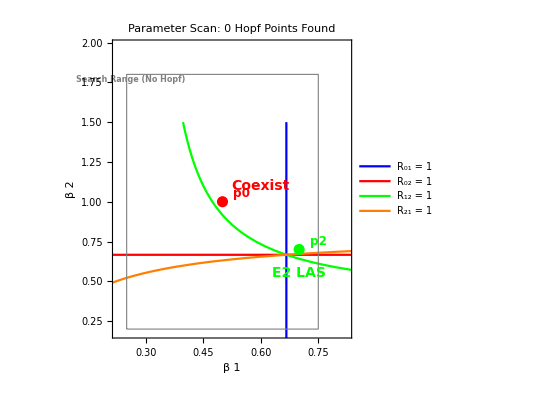

```mathematica
plotInd={3,4};
ploR[par_,coP_,R0A_,E0_,E1_,E2_,R12_,R21_,plotInd_:{1,2}]:=
Module[{p0,coPsec,bifP,bifVars,eqs,eqL,p0Values,f1,f2,p1,p2,p1Values,p2Values,f0e,p0e,plot,cop0},bifP=par[[plotInd]];
p0=coP[[plotInd]];
(*Remove β₁ and β₂ rules so ContourPlot can vary them*)coPsec=Delete[coP,List/@plotInd];
Print["bif param=",bifP," coPsec = ",coPsec,"p0=",p0];
R1s=(R0A[[1]]/. E0)//Factor;R2s=(R0A[[2]]/. E0)//Factor;R12s=(R12/. E2)//Factor;R21s=(R21/. E1)//Factor;
(*Print["R1s=R0A[[1]] /. E0  = ",R1s];
Print["R2s=R0A[[2]] /. E0  = ",R2s];
Print["R12s=R12 /. E2  = ",R12s];
Print["R21s=R21 /. E1   = ",R21s];*);
eqL={R1s-1,R2s-1,R12s-1,R21s-1};
bifVars=Variables[eqL/. coPsec];
cp=Thread[bifVars>0];
eqs=Thread[(eqL/. coPsec)==0];
(*Use FindInstance for LAS E1 (strain 1 dominates)*)
f1=FindInstance[Join[cp,{(R21/. E1/. coPsec)<1,1<(R0A[[1]]/. E0/. coPsec),1<(R0A[[2]]/. E0/. coPsec)}],bifVars];
p1=If[f1=!={},bifVars/. f1[[1]],{0.5,0.5}];
(*Use FindInstance for LAS E2 (strain 2 dominates)*)
f2=FindInstance[Join[cp,{(R12/. E2/. coPsec)<1,1<(R0A[[1]]/. E0/. coPsec),1<(R0A[[2]]/. E0/. coPsec)}],bifVars];
p2=If[f2=!={},bifVars/. f2[[1]],{0.7,0.7}];
(*Find point in coexistence zone near boundary*)
f0e=FindInstance[Join[cp,{(R12/. E2/. coPsec)>1,(R21/. E1/. coPsec)==1.01,1<(R0A[[1]]/. E0/. coPsec),
1<(R0A[[2]]/. E0/. coPsec)}],bifVars];
p0e=If[f0e=!={},bifVars/. f0e[[1]],{0.7,0.7}];
(*Extract numerical values*)p0Values=bifVars/. p0;
p1Values=p1;
p2Values=p2;
Print["p0 coordinates: ",p0Values," p1 coordinates: ",p1Values," p2 coordinates: ",p2Values," p0e coordinates: ",p0e];
plot=ContourPlot[Evaluate[eqs],Evaluate@{bifVars[[1]],0,3/2},Evaluate@{bifVars[[2]],0,3/2},
ContourStyle->{Blue,Red,Green,Orange},PlotLegends->{"R₀₁ = 1","R₀₂ = 1","R₁₂ = 1","R₂₁ = 1"},
AxesLabel->{ToString[Subscript[β,1]],ToString[Subscript[β,2]]},PlotLabel->"Analytical Boundaries with Stability Points",
Epilog->{PointSize[0.02],(*p0 point*)Red,Point[p0Values],Text[Style["p0",FontSize->12,FontWeight->Bold],p0Values+{0.05,0.05}],
(*p0e point*)Magenta,Point[p0e],Text[Style["p0e",FontSize->12,FontWeight->Bold],p0e+{0.05,0.05}],
(*p1 point (strain 1 dominates)*)Blue,Point[p1Values],Text[Style["p1",FontSize->12,FontWeight->Bold],p1Values+{0.05,0.05}],
(*p2 point (strain 2 dominates)*)Green,Point[p2Values],Text[Style["p2",FontSize->12,FontWeight->Bold],p2Values+{0.05,0.05}],
(*Region labels*)(*E1 LAS region (near p1)*)Text[Style["E1 LAS",FontSize->14,FontWeight->Bold,FontColor->Blue],
{p1Values[[1]],p1Values[[2]]-0.15}],(*E2 LAS region (near p2)*)Text[Style["E2 LAS",
FontSize->14,FontWeight->Bold,FontColor->Green],{p2Values[[1]],p2Values[[2]]-0.15}],
(*E1 GAS region (just above β₁ axis)*)Text[Style["E1 GAS",FontSize->14,FontWeight->Bold,FontColor->Blue],{1.2,0.1}],
(*E2 GAS region (vertical downwards,near β₂ axis,smaller letters)*)Text[Style["E2 GAS",FontSize->12,
FontWeight->Bold,FontColor->Green],{0.1,1.2},{0,-1}],(*Coexist region (around p0)*)
Text[Style["Coexist",FontSize->14,FontWeight->Bold,FontColor->Red],{p0Values[[1]]+0.1,p0Values[[2]]+0.1}]}];
conEx=Join[coPsec,f0e[[1]]];
(*Return plot and p0e for testing*){plot,conEx}]

{plot,conEx}=ploR[par,coP,R0A,E0,E1,E2,R12,R21,plotInd];




scan = scanPar[RHS, var, par, coP, {3,4}, plot, 0.5, 0.8, 5, 0.5]
```

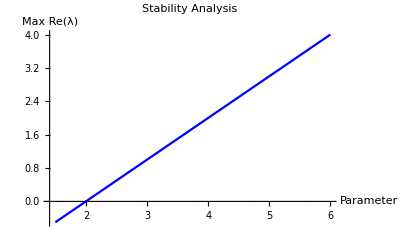

hopfD found no Hopf points

R₁₂ = 1.056, R₂₁ = 1.583

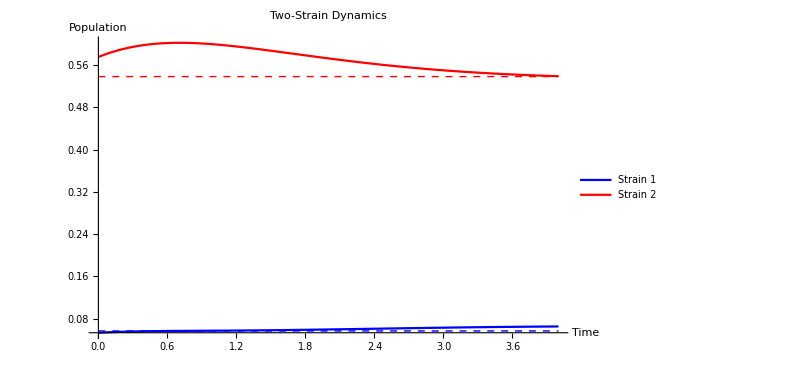

STABLE convergence

Curve: {<|Parameter→1.5,Equilibrium→{S→1.5,I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},Eigenvalues→{-2.,-2.,-2.,-2.,-1.25,-1.25,-1.,-0.5},MaxRealPart→-0.5,ComplexPairs→0|>,<|Parameter→1.725,Equilibrium→{S→1.725,I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},Eigenvalues→{-2.,-2.,-2.,-2.,-1.25,-1.1375,-1.,-0.275},MaxRealPart→-0.275,ComplexPairs→0|>,<|Parameter→1.95,Equilibrium→{S→1.95,I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},Eigenvalues→{-2.,-2.,-2.,-2.,-1.25,-1.025,-1.,-0.05},MaxRealPart→-0.05,ComplexPairs→0|>,<|Parameter→2.175,Equilibrium→{S→2.175,I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},Eigenvalues→{-2.,-2.,-2.,-2.,-1.25,-1.,-0.9125,0.175},MaxRealPart→0.175,ComplexPairs→0|>,<|Parameter→2.4,Equilibrium→{S→2.4,I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},Eigenvalues→{-2.,-2.,-2.,-2.,-1.25,-1.,-0.8,0.4},MaxRealPart→0.4,ComplexPairs→0|>,<|Parameter→2.625,Equilibrium→{S→2.625,I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},Eigenvalues→{-2.,-2.,-2.,-2.,-1.25,-1.,-0.6875,0.625},MaxRealPart→0.625,ComplexPairs→0|>,<|Parameter→2.85,Equilibrium→{S→2.85,I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},Eigenvalues→{-2.,-2.,-2.,-2.,-1.25,-1.,0.85,-0.575},MaxRealPart→0.85,ComplexPairs→0|>,<|Parameter→3.075,Equilibrium→{S→3.075,I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},Eigenvalues→{-2.,-2.,-2.,-2.,-1.25,1.075,-1.,-0.4625},MaxRealPart→1.075,ComplexPairs→0|>,<|Parameter→3.3,Equilibrium→{S→3.3,I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},Eigenvalues→{-2.,-2.,-2.,-2.,1.3,-1.25,-1.,-0.35},MaxRealPart→1.3,ComplexPairs→0|>,<|Parameter→3.525,Equilibrium→{S→3.525,I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},Eigenvalues→{-2.,-2.,-2.,-2.,1.525,-1.25,-1.,-0.2375},MaxRealPart→1.525,ComplexPairs→0|>,<|Parameter→3.75,Equilibrium→{S→3.75,I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},Eigenvalues→{-2.,-2.,-2.,-2.,1.75,-1.25,-1.,-0.125},MaxRealPart→1.75,ComplexPairs→0|>,<|Parameter→3.975,Equilibrium→{S→3.975,I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},Eigenvalues→{-2.,-2.,-2.,-2.,1.975,-1.25,-1.,-0.0125},MaxRealPart→1.975,ComplexPairs→0|>,<|Parameter→4.2,Equilibrium→{S→4.2,I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},Eigenvalues→{2.2,-2.,-2.,-2.,-2.,-1.25,-1.,0.1},MaxRealPart→2.2,ComplexPairs→0|>,<|Parameter→4.425,Equilibrium→{S→4.425,I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},Eigenvalues→{2.425,-2.,-2.,-2.,-2.,-1.25,-1.,0.2125},MaxRealPart→2.425,ComplexPairs→0|>,<|Parameter→4.65,Equilibrium→{S→4.65,I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},Eigenvalues→{2.65,-2.,-2.,-2.,-2.,-1.25,-1.,0.325},MaxRealPart→2.65,ComplexPairs→0|>,<|Parameter→4.875,Equilibrium→{S→4.875,I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},Eigenvalues→{2.875,-2.,-2.,-2.,-2.,-1.25,-1.,0.4375},MaxRealPart→2.875,ComplexPairs→0|>,<|Parameter→5.1,Equilibrium→{S→5.1,I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},Eigenvalues→{3.1,-2.,-2.,-2.,-2.,-1.25,-1.,0.55},MaxRealPart→3.1,ComplexPairs→0|>,<|Parameter→5.325,Equilibrium→{S→5.325,I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},Eigenvalues→{3.325,-2.,-2.,-2.,-2.,-1.25,-1.,0.6625},MaxRealPart→3.325,ComplexPairs→0|>,<|Parameter→5.55,Equilibrium→{S→5.55,I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},Eigenvalues→{3.55,-2.,-2.,-2.,-2.,-1.25,-1.,0.775},MaxRealPart→3.55,ComplexPairs→0|>,<|Parameter→5.775,Equilibrium→{S→5.775,I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},Eigenvalues→{3.775,-2.,-2.,-2.,-2.,-1.25,-1.,0.8875},MaxRealPart→3.775,ComplexPairs→0|>,<|Parameter→6.,Equilibrium→{S→6.,I1→0.,Y1→0.,R1→0.,I2→0.,Y2→0.,R2→0.,R→0.},Eigenvalues→{4.,-2.,-2.,-2.,-2.,-1.25,-1.,1.},MaxRealPart→4.,ComplexPairs→0|>}

Hopf points: {}

Equilibria found: <|E0→{S→3.,I1→0,Y1→0,R1→0,I2→0,Y2→0,R2→0,R→0},E2→{S→2.,I1→0,Y1→0,R1→0,I2→0.555556,Y2→0,R2→0.444444,R→0},E4→{S→1.94424,I1→0.0569524,Y1→0.0120438,R1→0.022304,I2→0.538028,Y2→0.00617217,R2→0.411152,R→0.009108}|>

Length of equilibria: 3

```mathematica
(* Detect Hopf bifurcations *)
hopfPoints = hopfD[curve];
TS[RHS, var, coP, R12, R21, 100]
Print["Curve: ",curve]
Print["Hopf points: ",hopfPoints]

Print["Equilibria found: ",equ]
Print["Length of equilibria: ",Length[equ]]
```

bif param={β_1,β_2} coPsec = {Λ→3,μ→1,γ_1→1,γ_2→1,η_1→5,η_2→5/2,θ_1→1,θ_2→1/4,θ_3→1,σ_1→1,σ_2→1}p0={β_1→1/2,β_2→1}

R1s=R0A[[1]] /. E0  = (Λ β_1)/(μ (μ+γ_1))

R2s=R0A[[2]] /. E0  = (Λ β_2)/(μ (μ+γ_2))

R12s=R12 /. E2  = (β_1 (μ^3+2 μ^2 γ_2+μ γ_2^2+μ^2 θ_2+μ γ_2 θ_2-μ^2 γ_2 η_1 σ_1+Λ β_2 γ_2 η_1 σ_1-μ γ_2^2 η_1 σ_1))/(μ β_2 (μ+γ_1) (μ+γ_2+θ_2))

R21s=R21 /. E1   = (β_2 (μ^3+2 μ^2 γ_1+μ γ_1^2+μ^2 θ_1+μ γ_1 θ_1-μ^2 γ_1 η_2 σ_2+Λ β_1 γ_1 η_2 σ_2-μ γ_1^2 η_2 σ_2))/(μ β_1 (μ+γ_2) (μ+γ_1+θ_1))

p0 coordinates: {1/2,1} p1 coordinates: {3,3/4} p2 coordinates: {0.7,0.7} p0e coordinates: {1.46667,0.740667}

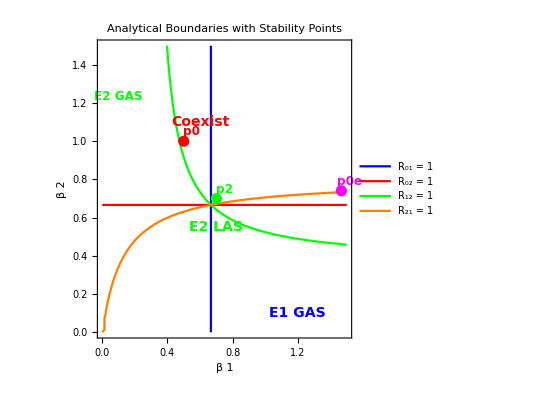

10real solutions found

Positive solutions (coexistence): 1

Using equilibrium: {1.34761,1.08951,0.00259162,0.541065,0.00919019,0.00368986,0.00320556,0.00314074}

Eigenvalues: {-2.9329,-1.81984+1.16371 ⅈ,-1.81984-1.16371 ⅈ,-2.02548+0.518927 ⅈ,-2.02548-0.518927 ⅈ,-1.86756,-1.,-0.0200949}

Result:Complex eigenvalues but not near Hopf conditions (stable spiral)

{{{1.34761,1.08951,0.00259162,0.541065,0.00919019,0.00368986,0.00320556,0.00314074}}}

```mathematica
bifInd={3,4};
par=Par[RHS,var];
ploR[par_,coP_,R0A_,E0_,E1_,E2_,R12_,R21_,bifInd_:{1,2}]:=Module[{p0,coPsec,bifP,bifVars,eqs,eqL,p0Values,f1,f2,p1,p2,p1Values,p2Values,f0e,p0e,plot,cop0},bifP=par[[bifInd]];
p0=coP[[bifInd]];
(*Remove β₁ and β₂ rules so ContourPlot can vary them*)coPsec=Delete[coP,List/@bifInd];
Print["bif param=",bifP," coPsec = ",coPsec,"p0=",p0];
Print["R1s=R0A[[1]] /. E0  = ",R1s=(R0A[[1]]/. E0)//Factor];
Print["R2s=R0A[[2]] /. E0  = ",R2s=(R0A[[2]]/. E0)//Factor];
Print["R12s=R12 /. E2  = ",R12s=(R12/. E2)//Factor];
Print["R21s=R21 /. E1   = ",R21s=(R21/. E1)//Factor];
eqL={R1s-1,R2s-1,R12s-1,R21s-1};
bifVars=Variables[eqL/. coPsec];
cp=Thread[bifVars>0];
eqs=Thread[(eqL/. coPsec)==0];
(*Use FindInstance for LAS E1 (strain 1 dominates)*)f1=FindInstance[Join[cp,{(R21/. E1/. coPsec)<1,1<(R0A[[1]]/. E0/. coPsec),1<(R0A[[2]]/. E0/. coPsec)}],bifVars];
p1=If[f1=!={},bifVars/. f1[[1]],{0.5,0.5}];
(*Use FindInstance for LAS E2 (strain 2 dominates)*)f2=FindInstance[Join[cp,{(R12/. E2/. coPsec)<1,1<(R0A[[1]]/. E0/. coPsec),1<(R0A[[2]]/. E0/. coPsec)}],bifVars];
p2=If[f2=!={},bifVars/. f2[[1]],{0.7,0.7}];
(*Find point in coexistence zone near boundary*)f0e=FindInstance[Join[cp,{(R12/. E2/. coPsec)>1,(R21/. E1/. coPsec)==1.01,1<(R0A[[1]]/. E0/. coPsec),1<(R0A[[2]]/. E0/. coPsec)}],bifVars];
p0e=If[f0e=!={},bifVars/. f0e[[1]],{0.7,0.7}];
(*Extract numerical values*)p0Values=bifVars/. p0;
p1Values=p1;
p2Values=p2;
Print["p0 coordinates: ",p0Values," p1 coordinates: ",p1Values," p2 coordinates: ",p2Values," p0e coordinates: ",p0e];
plot=ContourPlot[Evaluate[eqs],Evaluate@{bifVars[[1]],0,3/2},Evaluate@{bifVars[[2]],0,3/2},ContourStyle->{Blue,Red,Green,Orange},PlotLegends->{"R₀₁ = 1","R₀₂ = 1","R₁₂ = 1","R₂₁ = 1"},AxesLabel->{ToString[Subscript[β,1]],ToString[Subscript[β,2]]},PlotLabel->"Analytical Boundaries with Stability Points",Epilog->{PointSize[0.02],(*p0 point*)Red,Point[p0Values],Text[Style["p0",FontSize->12,FontWeight->Bold],p0Values+{0.05,0.05}],(*p0e point*)Magenta,Point[p0e],Text[Style["p0e",FontSize->12,FontWeight->Bold],p0e+{0.05,0.05}],(*p1 point (strain 1 dominates)*)Blue,Point[p1Values],Text[Style["p1",FontSize->12,FontWeight->Bold],p1Values+{0.05,0.05}],(*p2 point (strain 2 dominates)*)Green,Point[p2Values],Text[Style["p2",FontSize->12,FontWeight->Bold],p2Values+{0.05,0.05}],(*Region labels*)(*E1 LAS region (near p1)*)Text[Style["E1 LAS",FontSize->14,FontWeight->Bold,FontColor->Blue],{p1Values[[1]],p1Values[[2]]-0.15}],(*E2 LAS region (near p2)*)Text[Style["E2 LAS",FontSize->14,FontWeight->Bold,FontColor->Green],{p2Values[[1]],p2Values[[2]]-0.15}],(*E1 GAS region (just above β₁ axis)*)Text[Style["E1 GAS",FontSize->14,FontWeight->Bold,FontColor->Blue],{1.2,0.1}],(*E2 GAS region (vertical downwards,near β₂ axis,smaller letters)*)Text[Style["E2 GAS",FontSize->12,FontWeight->Bold,FontColor->Green],{0.1,1.2},{0,-1}],(*Coexist region (around p0)*)Text[Style["Coexist",FontSize->14,FontWeight->Bold,FontColor->Red],{p0Values[[1]]+0.1,p0Values[[2]]+0.1}]}];conEx=Join[coPsec,f0e[[1]]];
(*Return plot and p0e for testing*){plot,conEx}]

{plot,conEx}=ploR[par,coP,R0A,E0,E1,E2,R12,R21,bifInd];
plot
fpHopf[RHS,var,conEx]
```

```mathematica
(* Create Figure 1 style plot *)
(*fig1 = createFigure1[RHS, var, coP, R12, R21, par,
  BifurcationParameter -> θ1,
  ParameterRange -> {0, 0.5},
  NumPoints -> 100,
  PlotVariables -> {I1, I2, Y1, Y2},
  ShowHopf -> True
];

(* Or create custom bifurcation diagram *)
customPlot = plotBifurcationDiagram[curve, hopfPoints, θ1,
  FrameLabel -> {"Waning Rate θ₁", "Infected Population"},
  PlotStyle -> {Blue, Red, Green, Purple}
]*)
```

```mathematica
quickBifurcationPlot[curve,hopfPoints]
```

-Graphics-

```mathematica
(*Define parameter values as rules*)parValues={Λ->0.1,μ->0.01,Subscript[β,1]->0.5,Subscript[β,2]->0.4,Subscript[γ,1]->0.1,Subscript[γ,2]->0.1,Subscript[η,1]->0.8,Subscript[η,2]->0.8,Subscript[θ,1]->0.05,Subscript[θ,2]->0.05,Subscript[θ,3]->0.02,Subscript[σ,1]->0.7,Subscript[σ,2]->0.7};

createFigure1[RHS,var,coP,R12,R21,parValues,BifurcationParameter->Subscript[θ,1],ParameterRange->{0,0.2}]
```

-Graphics-

```mathematica
plotBifurcationDiagram[curve,hopfPoints,Subscript[θ,1]]
```

-Graphics-